```mathematica
ImportString@@{"2.0658746e+00","CSV"}
```

{{2.06587}}

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
import[fname_]:=ReadList[fname,String]//ImportString@@{#,"CSV"}&/@#&//Flatten
```

```mathematica
xs=import["ex2x.dat"]
```

{2.06587,2.36841,2.53999,2.54208,2.54908,2.78669,2.91168,3.03563,3.11467,3.15824,3.32759,3.37932,3.4122,3.42158,3.53157,3.6393,3.67325,3.92565,4.04986,4.24833,4.34401,4.38265,4.42306,4.61024,4.68812,4.97773,5.036,5.06845,5.41615,5.43956,5.45632,5.56985,5.60157,5.68776,5.72156,5.85389,6.1978,6.35109,6.4797,6.73838,6.86377,7.02234,7.07824,7.15142,7.4664,7.59739,7.74407,7.77297,7.82645,7.93064}

```mathematica
ys=import["ex2y.dat"]
```

{0.779189,0.915968,0.905384,0.905661,0.938989,0.966847,0.964368,0.914459,0.939339,0.96075,0.898371,0.912097,0.942385,0.966246,1.05265,1.01438,0.959694,0.968537,1.07661,1.1455,1.03406,1.007,0.966836,1.08959,1.06345,1.12372,1.03234,1.08745,1.0703,1.16065,1.0778,1.10698,1.09719,1.16486,1.14118,1.08442,1.12525,1.11683,1.19708,1.20695,1.1251,1.12357,1.21328,1.25227,1.24971,1.17997,1.18973,1.30299,1.26011,1.25623}

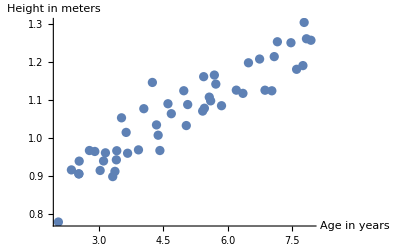

```mathematica
ListPlot[MapThread[List,{xs,ys}],AxesLabel->{"Age in years","Height in meters"}]
```